```mathematica
<<MaTeX`
```

## CollinsSoperK . f90

```mathematica
dataIN={{    0.010000,    0.345566,        0.978532,       -0.248283},
{    0.012589,    0.379196,        0.998371,       -0.236311},
{    0.015849,    0.415375,        1.013547,       -0.223903},
{    0.019953,    0.454067,        1.023447,       -0.211028},
{    0.025119,    0.495181,        1.027476,       -0.197653},
{    0.031623,    0.538565,        1.025083,       -0.183743},
{    0.039811,    0.583992,        1.015789,       -0.169259},
{    0.050119,    0.631143,        0.999227,       -0.154161},
{    0.063096,    0.679589,        0.975186,       -0.138405},
{    0.079433,    0.728762,        0.943664,       -0.121948},
{    0.100000,    0.777943,        0.904907,       -0.104747},
{    0.125893,    0.826305,        0.859351,       -0.086755},
{    0.158489,    0.872928,        0.807543,       -0.067928},
{    0.199526,    0.916823,        0.750110,       -0.048220},
{    0.251189,    0.957969,        0.686073,       -0.026942},
{    0.316228,    0.996305,        0.612834,       -0.002704},
{    0.398107,    1.025094,        0.541754,        0.021419},
{    0.501187,    1.045596,        0.469288,        0.047318},
{    0.630957,    1.056037,        0.396908,        0.075348},
{    0.794328,    1.054480,        0.326635,        0.105768},
{    1.000000,    1.040464,        0.264219,        0.136871},
{    1.258925,    1.011380,        0.204439,        0.172388},
{    1.584893,    0.972857,        0.157738,        0.206500},
{    1.995262,    0.921102,        0.116764,        0.244317},
{    2.511886,    0.855369,        0.082038,        0.286843},
{    3.162278,    0.775619,        0.053985,        0.335271},
{    3.981072,    0.682733,        0.032661,        0.391283},
{    5.011872,    0.579132,        0.017707,        0.457239},
{    6.309574,    0.470028,        0.008346,        0.536270},
{    7.943282,    0.365025,        0.003298,        0.632274},
{   10.000000,    0.274212,        0.001047,        0.749593}};
```

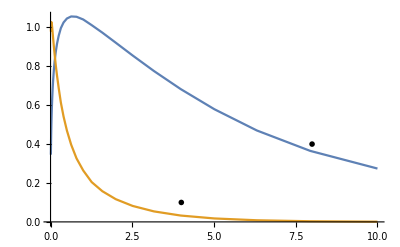

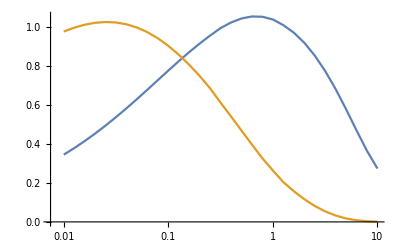

```mathematica
ListPlot[{dataIN⟦All,{1,2}⟧,dataIN⟦All,{1,3}⟧},Joined->True,Epilog->{
Inset[MaTeX["R[\\to 4\\text{GeV}]",Magnification->1.4],{8,0.4}],
Inset[MaTeX["R[\\to 91\\text{GeV}]",Magnification->1.4],{4,0.1}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,2}⟧,dataIN⟦All,{1,3}⟧},Joined->True]
```

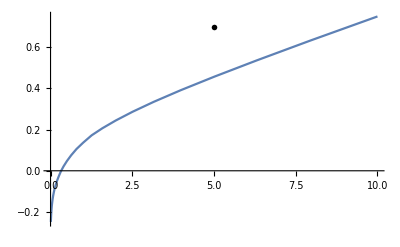

```mathematica
ListPlot[{dataIN⟦All,{1,4}⟧},Joined->True,Epilog->{
Inset[MaTeX["\\mathcal{D}(b,4\\text{GeV})",Magnification->1.4],{5,0.7}]
}]
```

## uTMDPDF . f90 (in b)

```mathematica
dataIN={{    0.010000,    8.944884,       12.525273,        3.091052,        4.328314,        8.752856,       12.256381},
{    0.012589,    8.955949,       12.513625,        3.396056,        4.745111,        8.941363,       12.493244},
{    0.015849,    8.964591,       12.497879,        3.723670,        5.191310,        9.086038,       12.667193},
{    0.019953,    8.970377,       12.477478,        4.073149,        5.665607,        9.180704,       12.770035},
{    0.025119,    8.972799,       12.451781,        4.443156,        6.165880,        9.219336,       12.793905},
{    0.031623,    8.971258,       12.420068,        4.831607,        6.689015,        9.196286,       12.731603},
{    0.039811,    8.964974,       12.381460,        5.235474,        7.230674,        9.106525,       12.576956},
{    0.050119,    8.952937,       12.334897,        5.650583,        7.785083,        8.946015,       12.325360},
{    0.063096,    8.933825,       12.279092,        6.071329,        8.344736,        8.712137,       11.974392},
{    0.079433,    8.905844,       12.212442,        6.490242,        8.899965,        8.404129,       11.524447},
{    0.100000,    8.866524,       12.132925,        6.897648,        9.438721,        8.023381,       10.979171},
{    0.125893,    8.812398,       12.037938,        7.281725,        9.947004,        7.572943,       10.344815},
{    0.158489,    8.738534,       11.924065,        7.628115,       10.408856,        7.056744,        9.629198},
{    0.199526,    8.637864,       11.786731,        7.919396,       10.806351,        6.479349,        8.841346},
{    0.251189,    8.500244,       11.619698,        8.142969,       11.131309,        5.831785,        7.971958},
{    0.316228,    8.311232,       11.414282,        8.280523,       11.372107,        5.093407,        6.995063},
{    0.398107,    8.050798,       11.158313,        8.252824,       11.438320,        4.361550,        6.045059},
{    0.501187,    7.692552,       10.834820,        8.043304,       11.328847,        3.610024,        5.084653},
{    0.630957,    7.204792,       10.420475,        7.608525,       11.004405,        2.859637,        4.135967},
{    0.794328,    6.556143,        9.884923,        6.913320,       10.423452,        2.141466,        3.228762},
{    1.000000,    5.728354,        9.192267,        5.960148,        9.564226,        1.513539,        2.428770},
{    1.258925,    4.736054,        8.307912,        4.789952,        8.402457,        0.968233,        1.698460},
{    1.584893,    3.643735,        7.213295,        3.544835,        7.017507,        0.574754,        1.137809},
{    1.995262,    2.562882,        5.929915,        2.360676,        5.462058,        0.299252,        0.692400},
{    2.511886,    1.617854,        4.539314,        1.383861,        3.882786,        0.132725,        0.372395},
{    3.162278,    0.897739,        3.178676,        0.696304,        2.465443,        0.048464,        0.171600},
{    3.981072,    0.426529,        1.998903,        0.291205,        1.364716,        0.013931,        0.065287},
{    5.011872,    0.167518,        1.105741,        0.097015,        0.640370,        0.002966,        0.019579},
{    6.309574,    0.051909,        0.524292,        0.024399,        0.246432,        0.000433,        0.004376},
{    7.943282,    0.011950,        0.205840,        0.004362,        0.075137,        0.000039,        0.000679},
{   10.000000,    0.001894,        0.063911,        0.000519,        0.017525,        0.000002,        0.000067}};
```

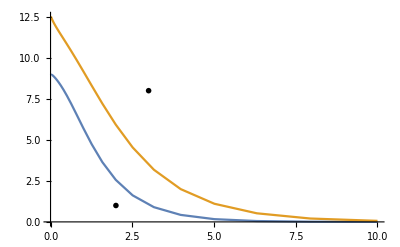

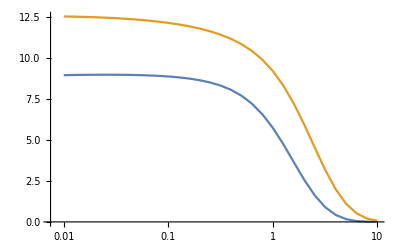

```mathematica
ListPlot[{dataIN⟦All,{1,2}⟧,dataIN⟦All,{1,3}⟧},Joined->True,Epilog->{
Inset[MaTeX["d-quark",Magnification->1.4],{2,1}],
Inset[MaTeX["u-quark",Magnification->1.4],{3,8}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,2}⟧,dataIN⟦All,{1,3}⟧},Joined->True]
```

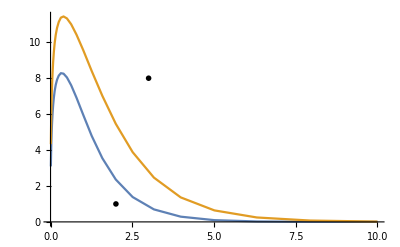

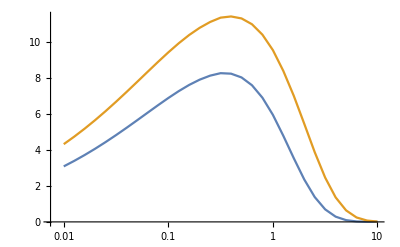

```mathematica
ListPlot[{dataIN⟦All,{1,4}⟧,dataIN⟦All,{1,5}⟧},Joined->True,Epilog->{
Inset[MaTeX["d-quark",Magnification->1.4],{2,1}],
Inset[MaTeX["u-quark",Magnification->1.4],{3,8}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,4}⟧,dataIN⟦All,{1,5}⟧},Joined->True]
```

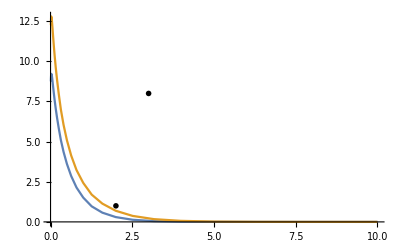

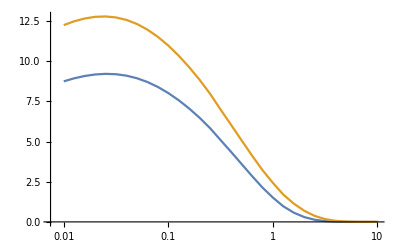

```mathematica
ListPlot[{dataIN⟦All,{1,6}⟧,dataIN⟦All,{1,7}⟧},Joined->True,Epilog->{
Inset[MaTeX["d-quark",Magnification->1.4],{2,1}],
Inset[MaTeX["u-quark",Magnification->1.4],{3,8}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,6}⟧,dataIN⟦All,{1,7}⟧},Joined->True]
```

## uTMDPDF . f90 (in kT)

```mathematica
dataIN={{    0.010000,    2.869285,        8.985124,        2.519290,        6.760045,        0.478725,        0.906423},
{    0.012589,    2.868959,        8.982594,        2.519074,        6.758823,        0.478709,        0.906370},
{    0.015849,    2.868444,        8.978587,        2.518731,        6.756887,        0.478683,        0.906286},
{    0.019953,    2.867628,        8.972242,        2.518187,        6.753821,        0.478642,        0.906154},
{    0.025119,    2.866335,        8.962199,        2.517327,        6.748966,        0.478577,        0.905944},
{    0.031623,    2.864288,        8.946321,        2.515964,        6.741282,        0.478474,        0.905611},
{    0.039811,    2.861048,        8.921247,        2.513805,        6.729134,        0.478311,        0.905084},
{    0.050119,    2.855925,        8.881738,        2.510391,        6.709952,        0.478054,        0.904251},
{    0.063096,    2.847836,        8.819695,        2.504993,        6.679729,        0.477646,        0.902932},
{    0.079433,    2.835090,        8.722777,        2.496476,        6.632273,        0.477001,        0.900850},
{    0.100000,    2.815074,        8.572636,        2.483067,        6.558156,        0.475981,        0.897568},
{    0.125893,    2.783809,        8.343025,        2.462041,        6.443365,        0.474374,        0.892410},
{    0.158489,    2.735376,        7.998773,        2.429273,        6.267868,        0.471846,        0.884347},
{    0.199526,    2.661311,        7.497858,        2.378691,        6.004815,        0.467890,        0.871837},
{    0.251189,    2.550274,        6.800344,        2.301762,        5.622049,        0.461743,        0.852663},
{    0.316228,    2.388711,        5.887632,        2.187384,        5.088693,        0.452296,        0.823811},
{    0.398107,    2.163749,        4.789085,        2.023004,        4.389513,        0.438024,        0.781589},
{    0.501187,    1.869452,        3.599502,        1.798185,        3.545451,        0.417013,        0.722273},
{    0.630957,    1.515539,        2.462310,        1.511369,        2.628648,        0.387235,        0.643615},
{    0.794328,    1.133036,        1.514221,        1.177973,        1.752640,        0.347249,        0.547078},
{    1.000000,    0.768634,        0.829394,        0.833333,        1.030659,        0.297328,        0.439566},
{    1.258925,    0.466589,        0.402714,        0.523194,        0.524829,        0.240493,        0.332540},
{    1.584893,    0.250320,        0.174807,        0.284012,        0.225632,        0.182405,        0.237787},
{    1.995262,    0.117344,        0.070751,        0.127851,        0.077125,        0.129521,        0.162483},
{    2.511886,    0.047821,        0.029270,        0.042962,        0.015744,        0.086491,        0.107369},
{    3.162278,    0.017297,        0.013524,        0.005762,       -0.005289,        0.054707,        0.068822},
{    3.981072,    0.006028,        0.006939,       -0.006296,       -0.010678,        0.032884,        0.042331},
{    5.011872,    0.002318,        0.003724,       -0.007948,       -0.010333,        0.018847,        0.024808},
{    6.309574,    0.001038,        0.002017,       -0.006299,       -0.007889,        0.010648,        0.014389},
{    7.943282,    0.000504,        0.001093,       -0.004295,       -0.005374,        0.006127,        0.008537},
{   10.000000,    0.000247,        0.000591,       -0.002973,       -0.003820,        0.003177,        0.004462}};
```

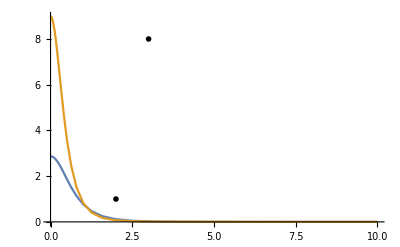

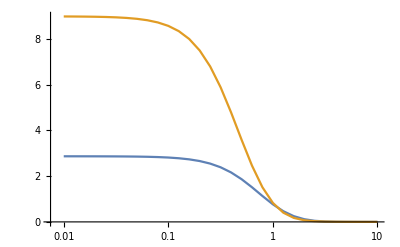

```mathematica
ListPlot[{dataIN⟦All,{1,2}⟧,dataIN⟦All,{1,3}⟧},Joined->True,Epilog->{
Inset[MaTeX["d-quark",Magnification->1.4],{2,1}],
Inset[MaTeX["u-quark",Magnification->1.4],{3,8}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,2}⟧,dataIN⟦All,{1,3}⟧},Joined->True]
```

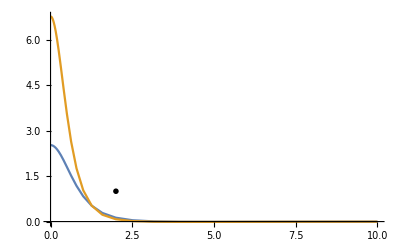

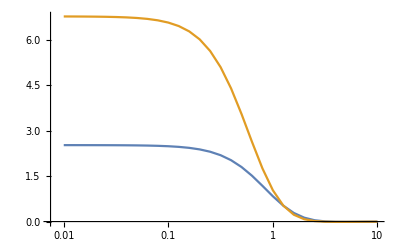

```mathematica
ListPlot[{dataIN⟦All,{1,4}⟧,dataIN⟦All,{1,5}⟧},Joined->True,Epilog->{
Inset[MaTeX["d-quark",Magnification->1.4],{2,1}],
Inset[MaTeX["u-quark",Magnification->1.4],{3,8}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,4}⟧,dataIN⟦All,{1,5}⟧},Joined->True]
```

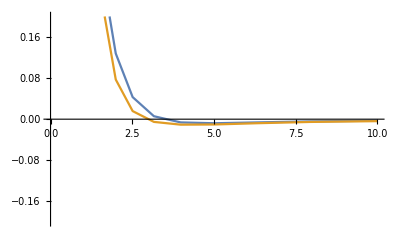

```mathematica
ListPlot[{dataIN⟦All,{1,4}⟧,dataIN⟦All,{1,5}⟧},Joined->True,PlotRange->{All,{-0.2,0.2}}]
```

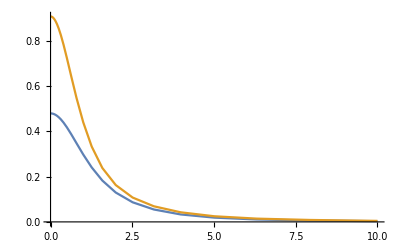

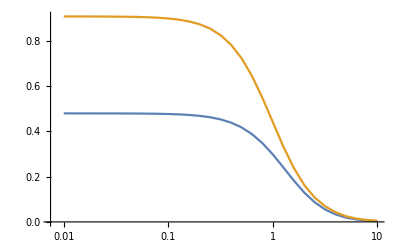

```mathematica
ListPlot[{dataIN⟦All,{1,6}⟧,dataIN⟦All,{1,7}⟧},Joined->True,Epilog->{
Inset[MaTeX["d-quark",Magnification->1.4],{2,1}],
Inset[MaTeX["u-quark",Magnification->1.4],{3,8}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,6}⟧,dataIN⟦All,{1,7}⟧},Joined->True]
```

## uTMDPDF . f90 (comparison of orders) (in b)

#### data

```mathematica
NA={{    0.010000,    0.999962,        0.999985,        0.345553,        0.345561,        0.978495,        0.978518},
{    0.012589,    0.999940,        0.999977,        0.379173,        0.379187,        0.998311,        0.998348},
{    0.015849,    0.999904,        0.999963,        0.415336,        0.415360,        1.013450,        1.013510},
{    0.019953,    0.999848,        0.999942,        0.453998,        0.454040,        1.023292,        1.023388},
{    0.025119,    0.999759,        0.999908,        0.495062,        0.495135,        1.027229,        1.027382},
{    0.031623,    0.999619,        0.999855,        0.538360,        0.538487,        1.024692,        1.024934},
{    0.039811,    0.999396,        0.999769,        0.583639,        0.583857,        1.015176,        1.015555},
{    0.050119,    0.999043,        0.999635,        0.630539,        0.630912,        0.998271,        0.998862},
{    0.063096,    0.998484,        0.999421,        0.678559,        0.679196,        0.973707,        0.974621},
{    0.079433,    0.997599,        0.999083,        0.727013,        0.728094,        0.941399,        0.942799},
{    0.100000,    0.996200,        0.998547,        0.774986,        0.776812,        0.901468,        0.903592},
{    0.125893,    0.993988,        0.997698,        0.821337,        0.824403,        0.854184,        0.857373},
{    0.158489,    0.990499,        0.996356,        0.864635,        0.869748,        0.799871,        0.804601},
{    0.199526,    0.985012,        0.994235,        0.903082,        0.911538,        0.738867,        0.745786},
{    0.251189,    0.976418,        0.990889,        0.935378,        0.949241,        0.669893,        0.679822},
{    0.316228,    0.963050,        0.985624,        0.959491,        0.981982,        0.590190,        0.604024},
{    0.398107,    0.942476,        0.977375,        0.966126,        1.001901,        0.510590,        0.529496},
{    0.501187,    0.911324,        0.964533,        0.952877,        1.008512,        0.427674,        0.452644},
{    0.630957,    0.865308,        0.944745,        0.913797,        0.997686,        0.343447,        0.374977},
{    0.794328,    0.799773,        0.914731,        0.843345,        0.964565,        0.261234,        0.298783},
{    1.000000,    0.711186,        0.870274,        0.739964,        0.905489,        0.187909,        0.229943},
{    1.258925,    0.599664,        0.806710,        0.606488,        0.815890,        0.122595,        0.164923},
{    1.584893,    0.471561,        0.720309,        0.458762,        0.700758,        0.074383,        0.113620},
{    1.995262,    0.339816,        0.610734,        0.313005,        0.562548,        0.039678,        0.071312},
{    2.511886,    0.220329,        0.483700,        0.188463,        0.413741,        0.018075,        0.039682},
{    3.162278,    0.125910,        0.351629,        0.097658,        0.272730,        0.006797,        0.018983},
{    3.981072,    0.061782,        0.230394,        0.042181,        0.157297,        0.002018,        0.007525},
{    5.011872,    0.025136,        0.133326,        0.014557,        0.077213,        0.000445,        0.002361},
{    6.309574,    0.008095,        0.066429,        0.003805,        0.031223,        0.000068,        0.000554},
{    7.943282,    0.001944,        0.027543,        0.000710,        0.010054,        0.000006,        0.000091},
{   10.000000,    0.000323,        0.009083,        0.000088,        0.002491,        0.000000,        0.000010}};
```

```mathematica
LO={{    0.010000,    9.076779,       12.701513,        3.136630,        4.389216,        8.881919,       12.428837},
{    0.012589,    9.092797,       12.697015,        3.447948,        4.814652,        9.077987,       12.676336},
{    0.015849,    9.106826,       12.689341,        3.782750,        5.270839,        9.230200,       12.861249},
{    0.019953,    9.118549,       12.678197,        4.140430,        5.756747,        9.332351,       12.975461},
{    0.025119,    9.127621,       12.663304,        4.519821,        6.270623,        9.378412,       13.011241},
{    0.031623,    9.133671,       12.644426,        4.919077,        6.809846,        9.362773,       12.961588},
{    0.039811,    9.136236,       12.621325,        5.335489,        7.370753,        9.280491,       12.820607},
{    0.050119,    9.134738,       12.593780,        5.765326,        7.948475,        9.127676,       12.584043},
{    0.063096,    9.128426,       12.561578,        6.203578,        8.536710,        8.901909,       12.249869},
{    0.079433,    9.116241,       12.524456,        6.643571,        9.127349,        8.602673,       11.818884},
{    0.100000,    9.096616,       12.482002,        7.076647,        9.710283,        8.231593,       11.295054},
{    0.125893,    9.067136,       12.433470,        7.492216,       10.273834,        7.791853,       10.684716},
{    0.158489,    9.023998,       12.377466,        7.877305,       10.804642,        7.287268,        9.995339},
{    0.199526,    8.961195,       12.311446,        8.215832,       11.287421,        6.721883,        9.234940},
{    0.251189,    8.869327,       12.230963,        8.496539,       11.716882,        6.085003,        8.391330},
{    0.316228,    8.733988,       12.128521,        8.701717,       12.083707,        5.352487,        7.432772},
{    0.398107,    8.533890,       11.992015,        8.748039,       12.292942,        4.623267,        6.496719},
{    0.501187,    8.239298,       11.802659,        8.614980,       12.340816,        3.866606,        5.538849},
{    0.630957,    7.812189,       11.532434,        8.249958,       12.178674,        3.100718,        4.577312},
{    0.794328,    7.211239,       11.141989,        7.604106,       11.749002,        2.355444,        3.639364},
{    1.000000,    6.405123,       10.580573,        6.664302,       11.008709,        1.692354,        2.795587},
{    1.258925,    5.395299,        9.791994,        5.456698,        9.903429,        1.103009,        2.001864},
{    1.584893,    4.239108,        8.731314,        4.124048,        8.494323,        0.668667,        1.377257},
{    1.995262,    3.052606,        7.394601,        2.811762,        6.811183,        0.356434,        0.863423},
{    2.511886,    1.978076,        5.850885,        1.691984,        5.004663,        0.162277,        0.479994},
{    3.162278,    1.129847,        4.249951,        0.876331,        3.296345,        0.060995,        0.229433},
{    3.981072,    0.554178,        2.782830,        0.378356,        1.899929,        0.018100,        0.090891},
{    5.011872,    0.225394,        1.609537,        0.130533,        0.932134,        0.003991,        0.028500},
{    6.309574,    0.072571,        0.801596,        0.034110,        0.376773,        0.000606,        0.006690},
{    7.943282,    0.017423,        0.332248,        0.006360,        0.121279,        0.000057,        0.001096},
{   10.000000,    0.002891,        0.109540,        0.000793,        0.030037,        0.000003,        0.000115}};
NLO={{    0.010000,    9.006935,       12.600142,        3.112494,        4.354186,        8.813574,       12.329643},
{    0.012589,    9.022309,       12.593547,        3.421219,        4.775417,        9.007614,       12.573036},
{    0.015849,    9.035640,       12.583315,        3.753182,        5.226798,        9.158050,       12.753786},
{    0.019953,    9.046531,       12.568937,        4.107728,        5.707136,        9.258643,       12.863639},
{    0.025119,    9.054510,       12.549837,        4.483618,        6.214436,        9.303291,       12.894656},
{    0.031623,    9.059025,       12.525379,        4.878875,        6.745732,        9.286254,       12.839555},
{    0.039811,    9.059358,       12.494796,        5.290593,        7.296862,        9.202399,       12.692081},
{    0.050119,    9.054585,       12.457192,        5.714738,        7.862269,        9.047585,       12.447561},
{    0.063096,    9.043514,       12.411519,        6.145872,        8.434732,        8.819104,       12.103533},
{    0.079433,    9.024543,       12.356527,        6.576745,        9.004969,        8.516140,       11.660416},
{    0.100000,    8.995486,       12.290703,        6.997974,        9.561463,        8.140080,       11.121945},
{    0.125893,    8.953279,       12.212152,        7.398136,       10.090958,        7.694010,       10.494525},
{    0.158489,    8.893518,       12.118400,        7.763406,       10.578496,        7.181901,        9.786132},
{    0.199526,    8.809770,       12.006049,        8.077003,       11.007427,        6.608297,        9.005859},
{    0.251189,    8.692544,       11.870213,        8.327187,       11.371294,        5.963717,        8.143829},
{    0.316228,    8.527893,       11.703593,        8.496383,       11.660349,        5.226184,        7.172362},
{    0.398107,    8.295796,       11.495179,        8.503970,       11.783639,        4.494279,        6.227557},
{    0.501187,    7.968901,       11.228501,        8.332253,       11.740479,        3.739711,        5.269403},
{    0.630957,    7.512957,       10.879478,        7.933959,       11.489129,        2.981950,        4.318149},
{    0.794328,    6.891874,       10.414862,        7.267342,       10.982261,        2.251128,        3.401859},
{    1.000000,    6.080472,        9.792694,        6.326514,       10.188949,        1.606575,        2.587414},
{    1.258925,    5.085546,        8.968266,        5.143420,        9.070326,        1.039683,        1.833462},
{    1.584893,    3.966060,        7.909198,        3.858411,        7.694521,        0.625597,        1.247579},
{    1.995262,    2.833946,        6.621926,        2.610354,        6.099470,        0.330903,        0.773202},
{    2.511886,    1.821777,        5.177700,        1.558290,        4.428842,        0.149455,        0.424767},
{    3.162278,    1.032103,        3.715380,        0.800519,        2.881721,        0.055718,        0.200574},
{    3.981072,    0.502051,        2.402677,        0.342767,        1.640386,        0.016398,        0.078475},
{    5.011872,    0.202486,        1.372158,        0.117266,        0.794661,        0.003585,        0.024297},
{    6.309574,    0.064646,        0.674639,        0.030385,        0.317099,        0.000540,        0.005631},
{    7.943282,    0.015389,        0.276005,        0.005617,        0.100749,        0.000051,        0.000910},
{   10.000000,    0.002532,        0.089805,        0.000694,        0.024625,        0.000003,        0.000094}};
NNLO={{    0.010000,    8.944884,       12.525273,        3.091052,        4.328314,        8.752856,       12.256381},
{    0.012589,    8.955949,       12.513625,        3.396056,        4.745111,        8.941363,       12.493244},
{    0.015849,    8.964591,       12.497879,        3.723670,        5.191310,        9.086038,       12.667193},
{    0.019953,    8.970377,       12.477478,        4.073149,        5.665607,        9.180704,       12.770035},
{    0.025119,    8.972799,       12.451781,        4.443156,        6.165880,        9.219336,       12.793905},
{    0.031623,    8.971258,       12.420068,        4.831607,        6.689015,        9.196286,       12.731603},
{    0.039811,    8.964974,       12.381460,        5.235474,        7.230674,        9.106525,       12.576956},
{    0.050119,    8.952937,       12.334897,        5.650583,        7.785083,        8.946015,       12.325360},
{    0.063096,    8.933825,       12.279092,        6.071329,        8.344736,        8.712137,       11.974392},
{    0.079433,    8.905844,       12.212442,        6.490242,        8.899965,        8.404129,       11.524447},
{    0.100000,    8.866524,       12.132925,        6.897648,        9.438721,        8.023381,       10.979171},
{    0.125893,    8.812398,       12.037938,        7.281725,        9.947004,        7.572943,       10.344815},
{    0.158489,    8.738534,       11.924065,        7.628115,       10.408856,        7.056744,        9.629198},
{    0.199526,    8.637864,       11.786731,        7.919396,       10.806351,        6.479349,        8.841346},
{    0.251189,    8.500244,       11.619698,        8.142969,       11.131309,        5.831785,        7.971958},
{    0.316228,    8.311232,       11.414282,        8.280523,       11.372107,        5.093407,        6.995063},
{    0.398107,    8.050798,       11.158313,        8.252824,       11.438320,        4.361550,        6.045059},
{    0.501187,    7.692552,       10.834820,        8.043304,       11.328847,        3.610024,        5.084653},
{    0.630957,    7.204792,       10.420475,        7.608525,       11.004405,        2.859637,        4.135967},
{    0.794328,    6.556143,        9.884923,        6.913320,       10.423452,        2.141466,        3.228762},
{    1.000000,    5.728354,        9.192267,        5.960148,        9.564226,        1.513539,        2.428770},
{    1.258925,    4.736054,        8.307912,        4.789952,        8.402457,        0.968233,        1.698460},
{    1.584893,    3.643735,        7.213295,        3.544835,        7.017507,        0.574754,        1.137809},
{    1.995262,    2.562882,        5.929915,        2.360676,        5.462058,        0.299252,        0.692400},
{    2.511886,    1.617854,        4.539314,        1.383861,        3.882786,        0.132725,        0.372395},
{    3.162278,    0.897739,        3.178676,        0.696304,        2.465443,        0.048464,        0.171600},
{    3.981072,    0.426529,        1.998903,        0.291205,        1.364716,        0.013931,        0.065287},
{    5.011872,    0.167518,        1.105741,        0.097015,        0.640370,        0.002966,        0.019579},
{    6.309574,    0.051909,        0.524292,        0.024399,        0.246432,        0.000433,        0.004376},
{    7.943282,    0.011950,        0.205840,        0.004362,        0.075137,        0.000039,        0.000679},
{   10.000000,    0.001894,        0.063911,        0.000519,        0.017525,        0.000002,        0.000067}};
N3LO={{    0.010000,    8.934424,       12.511632,        3.087437,        4.323600,        8.742620,       12.243032},
{    0.012589,    8.944197,       12.498367,        3.391600,        4.739325,        8.929630,       12.478011},
{    0.015849,    8.951311,       12.480723,        3.718153,        5.184184,        9.072578,       12.649805},
{    0.019953,    8.955279,       12.458072,        4.066294,        5.656795,        9.165252,       12.750174},
{    0.025119,    8.955519,       12.429695,        4.434599,        6.154944,        9.201581,       12.771212},
{    0.031623,    8.951343,       12.394762,        4.820881,        6.675386,        9.175871,       12.705662},
{    0.039811,    8.941855,       12.352260,        5.221972,        7.213621,        9.083041,       12.547294},
{    0.050119,    8.925901,       12.300953,        5.633520,        7.763660,        8.919000,       12.291442},
{    0.063096,    8.901976,       12.239331,        6.049685,        8.317714,        8.681078,       11.935618},
{    0.079433,    8.868054,       12.165501,        6.462702,        8.865756,        8.368467,       11.480151},
{    0.100000,    8.821374,       12.077064,        6.862524,        9.395264,        7.982525,       10.928622},
{    0.125893,    8.758108,       11.970916,        7.236866,        9.891623,        7.526290,       10.287219},
{    0.158489,    8.672874,       11.842996,        7.570799,       10.338089,        7.003721,        9.563732},
{    0.199526,    8.558068,       11.687893,        7.846236,       10.715734,        6.419493,        8.767207},
{    0.251189,    8.402947,       11.498322,        8.049761,       11.015035,        5.765032,        7.888685},
{    0.316228,    8.192496,       11.264357,        8.162225,       11.222736,        5.020642,        6.903184},
{    0.398107,    7.906331,       10.972494,        8.104732,       11.247837,        4.283285,        5.944390},
{    0.501187,    7.518300,       10.604570,        7.861106,       11.088099,        3.528250,        4.976600},
{    0.630957,    6.998094,       10.136662,        7.390244,       10.704687,        2.777597,        4.023319},
{    0.794328,    6.317602,        9.539187,        6.661784,       10.058881,        2.063550,        3.115833},
{    1.000000,    5.464165,        8.779499,        5.685268,        9.134756,        1.443735,        2.319709},
{    1.258925,    4.459804,        7.830021,        4.510558,        7.919128,        0.911757,        1.600760},
{    1.584893,    3.375832,        6.683608,        3.284203,        6.502197,        0.532496,        1.054257},
{    1.995262,    2.326348,        5.376428,        2.142804,        4.952239,        0.271633,        0.627773},
{    2.511886,    1.431290,        4.003293,        1.224280,        3.424291,        0.117420,        0.328421},
{    3.162278,    0.769019,        2.706089,        0.596466,        2.098895,        0.041515,        0.146088},
{    3.981072,    0.350861,        1.626478,        0.239544,        1.110450,        0.011460,        0.053123},
{    5.011872,    0.130918,        0.848648,        0.075819,        0.491479,        0.002318,        0.015027},
{    6.309574,    0.038000,        0.372692,        0.017861,        0.175176,        0.000317,        0.003111},
{    7.943282,    0.008037,        0.132006,        0.002934,        0.048185,        0.000027,        0.000435},
{   10.000000,    0.001138,        0.035512,        0.000312,        0.009738,        0.000001,        0.000037}};
```

#### plot

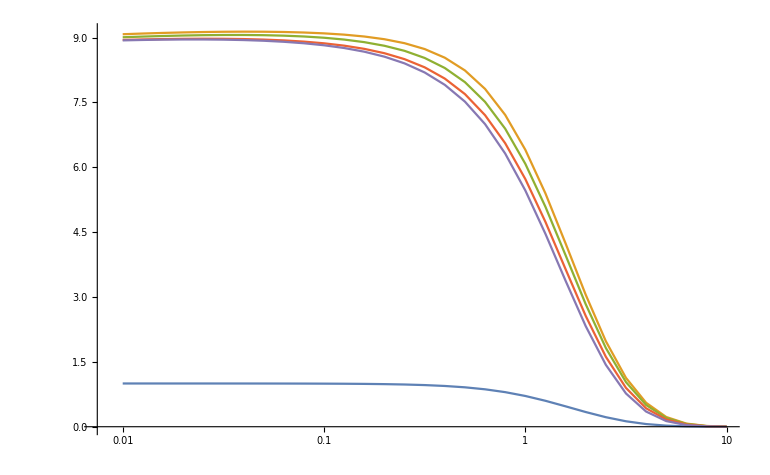

```mathematica
ListLogLinearPlot[{NA⟦All,{1,2}⟧,LO⟦All,{1,2}⟧,NLO⟦All,{1,2}⟧,NNLO⟦All,{1,2}⟧,N3LO⟦All,{1,2}⟧},Joined->True]
```

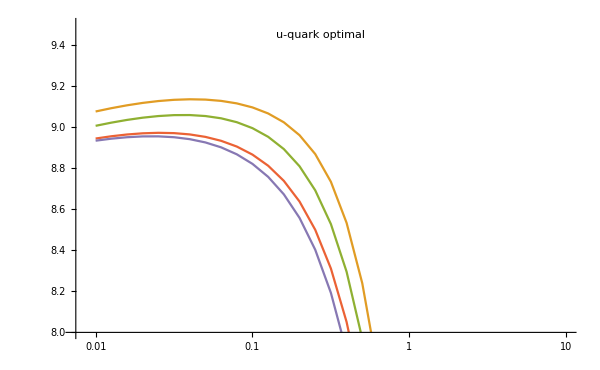
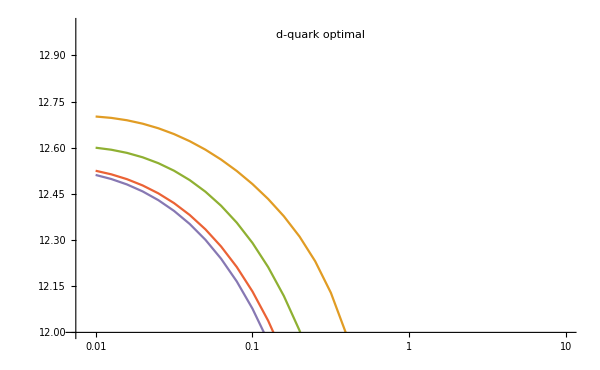

```mathematica
{ListLogLinearPlot[{NA⟦All,{1,2}⟧,LO⟦All,{1,2}⟧,NLO⟦All,{1,2}⟧,NNLO⟦All,{1,2}⟧,N3LO⟦All,{1,2}⟧},Joined->True,PlotRange->{8,9.5},ImageSize->600,Epilog->{Inset["u-quark optimal",Scaled[{0.5,0.95}]]}],
ListLogLinearPlot[{NA⟦All,{1,3}⟧,LO⟦All,{1,3}⟧,NLO⟦All,{1,3}⟧,NNLO⟦All,{1,3}⟧,N3LO⟦All,{1,3}⟧},Joined->True,PlotRange->{12,13.},ImageSize->600,
Epilog->{Inset["d-quark optimal",Scaled[{0.5,0.95}]]}]}
```

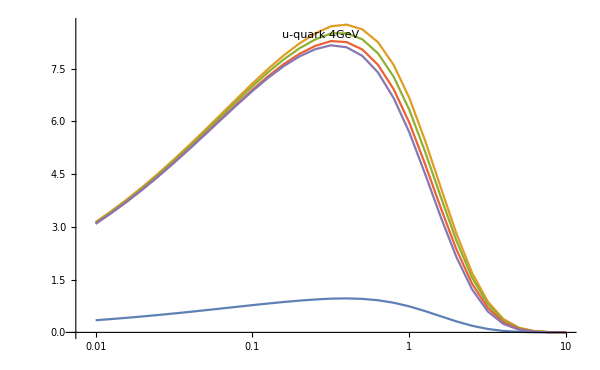

```mathematica
ListLogLinearPlot[{NA⟦All,{1,4}⟧,LO⟦All,{1,4}⟧,NLO⟦All,{1,4}⟧,NNLO⟦All,{1,4}⟧,N3LO⟦All,{1,4}⟧},Joined->True,ImageSize->600,
Epilog->{Inset["u-quark 4GeV",Scaled[{0.5,0.95}]]}]
```

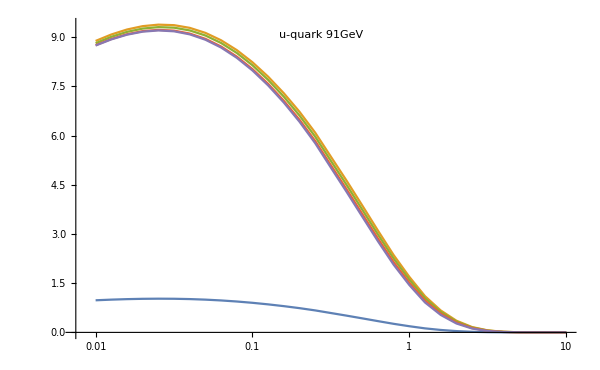

```mathematica
ListLogLinearPlot[{NA⟦All,{1,6}⟧,LO⟦All,{1,6}⟧,NLO⟦All,{1,6}⟧,NNLO⟦All,{1,6}⟧,N3LO⟦All,{1,6}⟧},Joined->True,ImageSize->600,
Epilog->{Inset["u-quark 91GeV",Scaled[{0.5,0.95}]]}]
```

## uTMDPDF . f90 (comparison of orders) (in kT)

#### data

```mathematica
NA={{    0.010000,    0.382292,        1.001345,        0.331174,        0.727108,        0.059895,        0.089234},
{    0.012589,    0.382244,        1.001020,        0.331143,        0.726959,        0.059893,        0.089228},
{    0.015849,    0.382169,        1.000504,        0.331094,        0.726722,        0.059889,        0.089219},
{    0.019953,    0.382050,        0.999688,        0.331017,        0.726347,        0.059884,        0.089204},
{    0.025119,    0.381861,        0.998396,        0.330894,        0.725754,        0.059875,        0.089181},
{    0.031623,    0.381562,        0.996354,        0.330699,        0.724815,        0.059861,        0.089144},
{    0.039811,    0.381089,        0.993131,        0.330391,        0.723331,        0.059839,        0.089085},
{    0.050119,    0.380341,        0.988056,        0.329904,        0.720989,        0.059804,        0.088993},
{    0.063096,    0.379161,        0.980094,        0.329134,        0.717300,        0.059749,        0.088847},
{    0.079433,    0.377302,        0.967678,        0.327918,        0.711515,        0.059661,        0.088616},
{    0.100000,    0.374384,        0.948492,        0.326006,        0.702494,        0.059523,        0.088252},
{    0.125893,    0.369831,        0.919270,        0.323010,        0.688556,        0.059305,        0.087681},
{    0.158489,    0.362790,        0.875728,        0.318345,        0.667329,        0.058963,        0.086790},
{    0.199526,    0.352049,        0.812969,        0.311157,        0.635697,        0.058427,        0.085409},
{    0.251189,    0.336010,        0.726803,        0.300255,        0.590071,        0.057596,        0.083299},
{    0.316228,    0.312810,        0.616320,        0.284112,        0.527301,        0.056321,        0.080137},
{    0.398107,    0.280790,        0.487010,        0.261057,        0.446484,        0.054400,        0.075542},
{    0.501187,    0.239433,        0.352034,        0.229814,        0.351287,        0.051585,        0.069151},
{    0.630957,    0.190572,        0.228804,        0.190476,        0.251163,        0.047621,        0.060796},
{    0.794328,    0.138991,        0.131568,        0.145566,        0.159321,        0.042348,        0.050744},
{    1.000000,    0.091282,        0.065757,        0.100233,        0.087386,        0.035850,        0.039837},
{    1.258925,    0.053120,        0.027879,        0.060646,        0.040108,        0.028576,        0.029326},
{    1.584893,    0.026917,        0.009683,        0.031221,        0.014356,        0.021298,        0.020365},
{    1.995262,    0.011600,        0.002625,        0.012862,        0.002988,        0.014833,        0.013529},
{    2.511886,    0.004111,        0.000521,        0.003470,       -0.000852,        0.009712,        0.008723},
{    3.162278,    0.001143,        0.000070,       -0.000265,       -0.001665,        0.006028,        0.005474},
{    3.981072,    0.000234,        0.000006,       -0.001224,       -0.001549,        0.003560,        0.003295},
{    5.011872,    0.000033,        0.000000,       -0.001156,       -0.001205,        0.002005,        0.001883},
{    6.309574,    0.000003,       -0.000000,       -0.000831,       -0.000827,        0.001120,        0.001073},
{    7.943282,    0.000000,        0.000000,       -0.000536,       -0.000527,        0.000645,        0.000635},
{   10.000000,    0.000000,       -0.000000,       -0.000358,       -0.000357,        0.000330,        0.000321}};
```

```mathematica
LO={{    0.010000,    3.436745,       12.113946,        2.978218,        8.803234,        0.539916,        1.084791},
{    0.012589,    3.436319,       12.110017,        2.977940,        8.801431,        0.539896,        1.084720},
{    0.015849,    3.435645,       12.103795,        2.977501,        8.798573,        0.539864,        1.084608},
{    0.019953,    3.434575,       12.093942,        2.976805,        8.794048,        0.539815,        1.084430},
{    0.025119,    3.432882,       12.078352,        2.975702,        8.786884,        0.539736,        1.084148},
{    0.031623,    3.430200,       12.053708,        2.973956,        8.775547,        0.539610,        1.083702},
{    0.039811,    3.425957,       12.014810,        2.971191,        8.757628,        0.539412,        1.082995},
{    0.050119,    3.419248,       11.953557,        2.966817,        8.729344,        0.539098,        1.081877},
{    0.063096,    3.408658,       11.857466,        2.959904,        8.684809,        0.538601,        1.080110},
{    0.079433,    3.391978,       11.707608,        2.948999,        8.614951,        0.537815,        1.077318},
{    0.100000,    3.365801,       11.476046,        2.931838,        8.506017,        0.536574,        1.072921},
{    0.125893,    3.324954,       11.123329,        2.904949,        8.337717,        0.534617,        1.066016},
{    0.158489,    3.261781,       10.597762,        2.863088,        8.081384,        0.531541,        1.055233},
{    0.199526,    3.165417,        9.840175,        2.798582,        7.699384,        0.526730,        1.038535},
{    0.251189,    3.021504,        8.799919,        2.700737,        7.148332,        0.519264,        1.013013},
{    0.316228,    2.813332,        7.465858,        2.555854,        6.390115,        0.507810,        0.974776},
{    0.398107,    2.525991,        5.904019,        2.348915,        5.413705,        0.490555,        0.919189},
{    0.501187,    2.154796,        4.273037,        2.068442,        4.263170,        0.465262,        0.841858},
{    0.630957,    1.716143,        2.782968,        1.715223,        3.052470,        0.429642,        0.740740},
{    0.794328,    1.252885,        1.605952,        1.311854,        1.941028,        0.382246,        0.619014},
{    1.000000,    0.824151,        0.807903,        0.904476,        1.069356,        0.323818,        0.486838},
{    1.258925,    0.480881,        0.347188,        0.548456,        0.495202,        0.258388,        0.359301},
{    1.584893,    0.244828,        0.124559,        0.283489,        0.181192,        0.192864,        0.250385},
{    1.995262,    0.106500,        0.037035,        0.117826,        0.041430,        0.134590,        0.167082},
{    2.511886,    0.038535,        0.009962,        0.032735,       -0.006805,        0.088350,        0.108310},
{    3.162278,    0.011327,        0.003330,       -0.001399,       -0.017924,        0.055021,        0.068401},
{    3.981072,    0.002774,        0.001721,       -0.010435,       -0.017398,        0.032618,        0.041496},
{    5.011872,    0.000701,        0.001086,       -0.010086,       -0.013801,        0.018460,        0.023964},
{    6.309574,    0.000265,        0.000697,       -0.007320,       -0.009582,        0.010358,        0.013798},
{    7.943282,    0.000136,        0.000439,       -0.004758,       -0.006156,        0.005975,        0.008232},
{   10.000000,    0.000071,        0.000269,       -0.003204,       -0.004221,        0.003070,        0.004237}};
NLO={{    0.010000,    3.191447,       10.593128,        2.776726,        7.784176,        0.511835,        0.990208},
{    0.012589,    3.191061,       10.589830,        2.776474,        7.782642,        0.511817,        0.990146},
{    0.015849,    3.190450,       10.584605,        2.776074,        7.780211,        0.511788,        0.990048},
{    0.019953,    3.189482,       10.576332,        2.775440,        7.776362,        0.511742,        0.989892},
{    0.025119,    3.187949,       10.563241,        2.774437,        7.770267,        0.511669,        0.989646},
{    0.031623,    3.185522,       10.542546,        2.772847,        7.760623,        0.511554,        0.989256},
{    0.039811,    3.181681,       10.509877,        2.770330,        7.745377,        0.511370,        0.988638},
{    0.050119,    3.175608,       10.458426,        2.766349,        7.721311,        0.511081,        0.987660},
{    0.063096,    3.166021,       10.377691,        2.760057,        7.683411,        0.510622,        0.986113},
{    0.079433,    3.150919,       10.251733,        2.750128,        7.623945,        0.509896,        0.983671},
{    0.100000,    3.127216,       10.056981,        2.734505,        7.531179,        0.508750,        0.979823},
{    0.125893,    3.090220,        9.760044,        2.710018,        7.387764,        0.506943,        0.973779},
{    0.158489,    3.032980,        9.316922,        2.671888,        7.169116,        0.504103,        0.964338},
{    0.199526,    2.945613,        8.676687,        2.613105,        6.842775,        0.499660,        0.949709},
{    0.251189,    2.815014,        7.794457,        2.523880,        6.370917,        0.492762,        0.927329},
{    0.316228,    2.625828,        6.657133,        2.391623,        5.719419,        0.482174,        0.893754},
{    0.398107,    2.364121,        5.315659,        2.202413,        4.876226,        0.466211,        0.844842},
{    0.501187,    2.024946,        3.900304,        1.945352,        3.875627,        0.442782,        0.776579},
{    0.630957,    1.622268,        2.589334,        1.620473,        2.812435,        0.409723,        0.686902},
{    0.794328,    1.194254,        1.535191,        1.247601,        1.823588,        0.365613,        0.578230},
{    1.000000,    0.794715,        0.803810,        0.868403,        1.034385,        0.311018,        0.459153},
{    1.258925,    0.471236,        0.368314,        0.533907,        0.502003,        0.249548,        0.342884},
{    1.584893,    0.245592,        0.148025,        0.281875,        0.200837,        0.187551,        0.242119},
{    1.995262,    0.110845,        0.054427,        0.121677,        0.059498,        0.131932,        0.163722},
{    2.511886,    0.042810,        0.020691,        0.037392,        0.005584,        0.087347,        0.107403},
{    3.162278,    0.014308,        0.009365,        0.002133,       -0.010524,        0.054858,        0.068528},
{    3.981072,    0.004505,        0.004979,       -0.008275,       -0.013261,        0.032787,        0.041991},
{    5.011872,    0.001605,        0.002804,       -0.008926,       -0.011588,        0.018701,        0.024511},
{    6.309574,    0.000710,        0.001584,       -0.006755,       -0.008473,        0.010543,        0.014203},
{    7.943282,    0.000348,        0.000886,       -0.004503,       -0.005637,        0.006077,        0.008458},
{   10.000000,    0.000169,        0.000489,       -0.003083,       -0.003961,        0.003136,        0.004397}};
NNLO={{    0.010000,    2.869285,        8.985124,        2.519290,        6.760045,        0.478725,        0.906423},
{    0.012589,    2.868959,        8.982594,        2.519074,        6.758823,        0.478709,        0.906370},
{    0.015849,    2.868444,        8.978587,        2.518731,        6.756887,        0.478683,        0.906286},
{    0.019953,    2.867628,        8.972242,        2.518187,        6.753821,        0.478642,        0.906154},
{    0.025119,    2.866335,        8.962199,        2.517327,        6.748966,        0.478577,        0.905944},
{    0.031623,    2.864288,        8.946321,        2.515964,        6.741282,        0.478474,        0.905611},
{    0.039811,    2.861048,        8.921247,        2.513805,        6.729134,        0.478311,        0.905084},
{    0.050119,    2.855925,        8.881738,        2.510391,        6.709952,        0.478054,        0.904251},
{    0.063096,    2.847836,        8.819695,        2.504993,        6.679729,        0.477646,        0.902932},
{    0.079433,    2.835090,        8.722777,        2.496476,        6.632273,        0.477001,        0.900850},
{    0.100000,    2.815074,        8.572636,        2.483067,        6.558156,        0.475981,        0.897568},
{    0.125893,    2.783809,        8.343025,        2.462041,        6.443365,        0.474374,        0.892410},
{    0.158489,    2.735376,        7.998773,        2.429273,        6.267868,        0.471846,        0.884347},
{    0.199526,    2.661311,        7.497858,        2.378691,        6.004815,        0.467890,        0.871837},
{    0.251189,    2.550274,        6.800344,        2.301762,        5.622049,        0.461743,        0.852663},
{    0.316228,    2.388711,        5.887632,        2.187384,        5.088693,        0.452296,        0.823811},
{    0.398107,    2.163749,        4.789085,        2.023004,        4.389513,        0.438024,        0.781589},
{    0.501187,    1.869452,        3.599502,        1.798185,        3.545451,        0.417013,        0.722273},
{    0.630957,    1.515539,        2.462310,        1.511369,        2.628648,        0.387235,        0.643615},
{    0.794328,    1.133036,        1.514221,        1.177973,        1.752640,        0.347249,        0.547078},
{    1.000000,    0.768634,        0.829394,        0.833333,        1.030659,        0.297328,        0.439566},
{    1.258925,    0.466589,        0.402714,        0.523194,        0.524829,        0.240493,        0.332540},
{    1.584893,    0.250320,        0.174807,        0.284012,        0.225632,        0.182405,        0.237787},
{    1.995262,    0.117344,        0.070751,        0.127851,        0.077125,        0.129521,        0.162483},
{    2.511886,    0.047821,        0.029270,        0.042962,        0.015744,        0.086491,        0.107369},
{    3.162278,    0.017297,        0.013524,        0.005762,       -0.005289,        0.054707,        0.068822},
{    3.981072,    0.006028,        0.006939,       -0.006296,       -0.010678,        0.032884,        0.042331},
{    5.011872,    0.002318,        0.003724,       -0.007948,       -0.010333,        0.018847,        0.024808},
{    6.309574,    0.001038,        0.002017,       -0.006299,       -0.007889,        0.010648,        0.014389},
{    7.943282,    0.000504,        0.001093,       -0.004295,       -0.005374,        0.006127,        0.008537},
{   10.000000,    0.000247,        0.000591,       -0.002973,       -0.003820,        0.003177,        0.004462}};
N3LO={{    0.010000,    2.571967,        7.486254,        2.288161,        5.845936,        0.451837,        0.839751},
{    0.012589,    2.571705,        7.484525,        2.287980,        5.845027,        0.451823,        0.839707},
{    0.015849,    2.571289,        7.481788,        2.287695,        5.843586,        0.451800,        0.839636},
{    0.019953,    2.570630,        7.477452,        2.287242,        5.841303,        0.451764,        0.839525},
{    0.025119,    2.569585,        7.470588,        2.286526,        5.837688,        0.451707,        0.839348},
{    0.031623,    2.567932,        7.459730,        2.285390,        5.831965,        0.451616,        0.839068},
{    0.039811,    2.565314,        7.442569,        2.283592,        5.822913,        0.451472,        0.838624},
{    0.050119,    2.561175,        7.415497,        2.280748,        5.808611,        0.451244,        0.837921},
{    0.063096,    2.554635,        7.372899,        2.276250,        5.786054,        0.450884,        0.836810},
{    0.079433,    2.544325,        7.306153,        2.269149,        5.750579,        0.450314,        0.835055},
{    0.100000,    2.528119,        7.202259,        2.257965,        5.695038,        0.449413,        0.832286},
{    0.125893,    2.502766,        7.042200,        2.240410,        5.608687,        0.447992,        0.827933},
{    0.158489,    2.463400,        6.799529,        2.213010,        5.475895,        0.445756,        0.821117},
{    0.199526,    2.402981,        6.440529,        2.170618,        5.275103,        0.442253,        0.810522},
{    0.251189,    2.311897,        5.928680,        2.105917,        4.979180,        0.436803,        0.794231},
{    0.316228,    2.178271,        5.237177,        2.009203,        4.559393,        0.428412,        0.769604},
{    0.398107,    1.989979,        4.370655,        1.869113,        3.995811,        0.415697,        0.733312},
{    0.501187,    1.739567,        3.386998,        1.675354,        3.294697,        0.396894,        0.681816},
{    0.630957,    1.431892,        2.397372,        1.424363,        2.505603,        0.370072,        0.612585},
{    0.794328,    1.090577,        1.529032,        1.126832,        1.721266,        0.333727,        0.526100},
{    1.000000,    0.755748,        0.870395,        0.811926,        1.047279,        0.287811,        0.427718},
{    1.258925,    0.469622,        0.440509,        0.520950,        0.554450,        0.234774,        0.327470},
{    1.584893,    0.258495,        0.199957,        0.290219,        0.250221,        0.179682,        0.236633},
{    1.995262,    0.124802,        0.084496,        0.135238,        0.092340,        0.128688,        0.162934},
{    2.511886,    0.052735,        0.035869,        0.048403,        0.023620,        0.086555,        0.108141},
{    3.162278,    0.019952,        0.016495,        0.008902,       -0.001591,        0.055040,        0.069464},
{    3.981072,    0.007288,        0.008266,       -0.004741,       -0.008990,        0.033214,        0.042797},
{    5.011872,    0.002881,        0.004329,       -0.007239,       -0.009563,        0.019097,        0.025131},
{    6.309574,    0.001292,        0.002300,       -0.005992,       -0.007550,        0.010801,        0.014577},
{    7.943282,    0.000622,        0.001227,       -0.004165,       -0.005231,        0.006201,        0.008621},
{   10.000000,    0.000305,        0.000658,       -0.002909,       -0.003746,        0.003227,        0.004522}};
```

#### plot

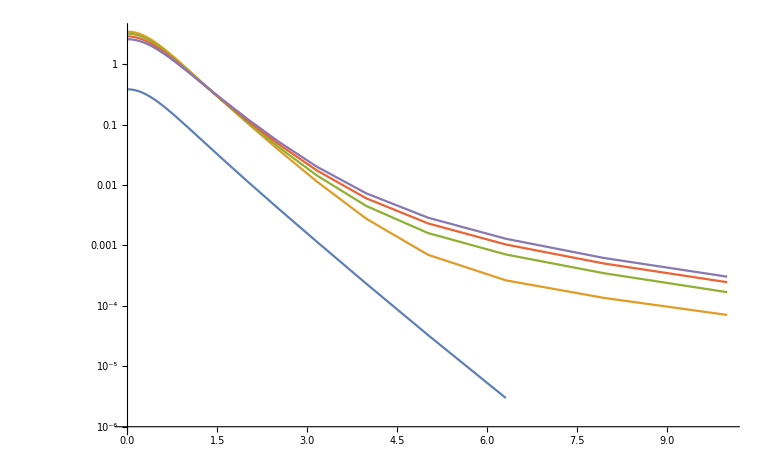

```mathematica
ListLogPlot[{NA⟦All,{1,2}⟧,LO⟦All,{1,2}⟧,NLO⟦All,{1,2}⟧,NNLO⟦All,{1,2}⟧,N3LO⟦All,{1,2}⟧},Joined->True]
```

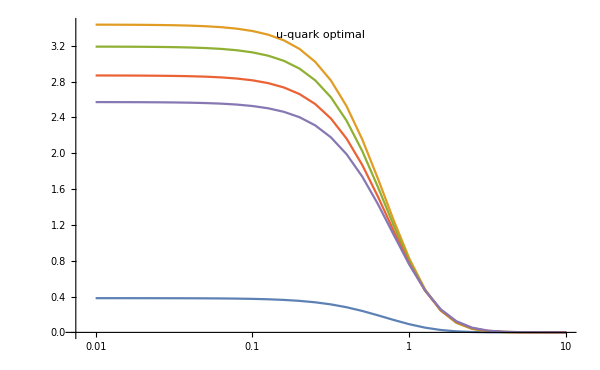
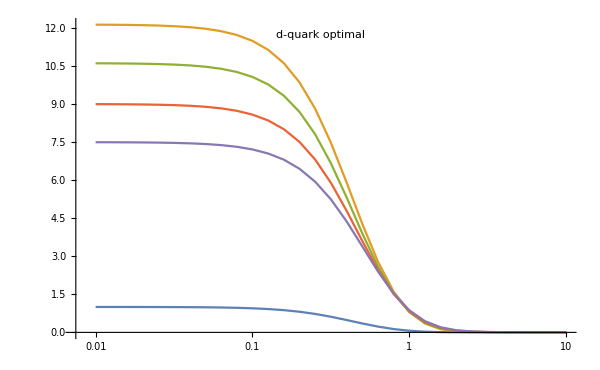

```mathematica
{ListLogLinearPlot[{NA⟦All,{1,2}⟧,LO⟦All,{1,2}⟧,NLO⟦All,{1,2}⟧,NNLO⟦All,{1,2}⟧,N3LO⟦All,{1,2}⟧},Joined->True,ImageSize->600,Epilog->{Inset["u-quark optimal",Scaled[{0.5,0.95}]]}],
ListLogLinearPlot[{NA⟦All,{1,3}⟧,LO⟦All,{1,3}⟧,NLO⟦All,{1,3}⟧,NNLO⟦All,{1,3}⟧,N3LO⟦All,{1,3}⟧},Joined->True,ImageSize->600,Epilog->{Inset["d-quark optimal",Scaled[{0.5,0.95}]]}]}
```

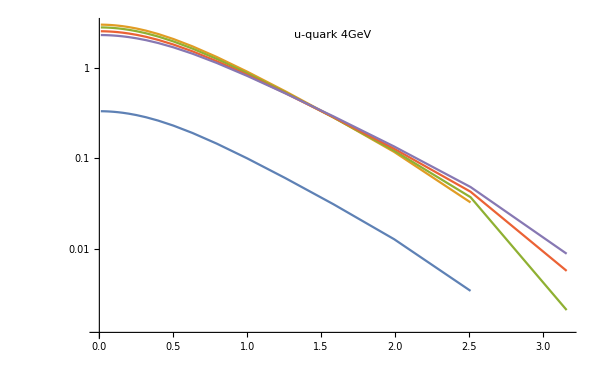

```mathematica
ListLogPlot[{NA⟦All,{1,4}⟧,LO⟦All,{1,4}⟧,NLO⟦All,{1,4}⟧,NNLO⟦All,{1,4}⟧,N3LO⟦All,{1,4}⟧},Joined->True,ImageSize->600,
Epilog->{Inset["u-quark 4GeV",Scaled[{0.5,0.95}]]}]
```

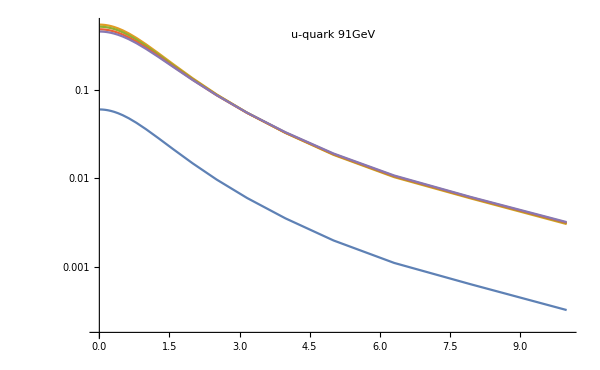

```mathematica
ListLogPlot[{NA⟦All,{1,6}⟧,LO⟦All,{1,6}⟧,NLO⟦All,{1,6}⟧,NNLO⟦All,{1,6}⟧,N3LO⟦All,{1,6}⟧},Joined->True,ImageSize->600,
Epilog->{Inset["u-quark 91GeV",Scaled[{0.5,0.95}]]}]
```

## xSec. f90

### Example of different DY - routines (Z-boson)

```mathematica
LIST={{0.50000000,9.9541053080},{1.50000000,26.3800924423},{2.50000000,35.8333600605},{3.50000000,39.2424776910},{4.50000000,39.3112031488},{5.50000000,37.4511727581},{6.50000000,34.9384511513},{7.50000000,32.3050690966},{8.50000000,29.6281558479},{9.50000000,27.1059907419}};
APROX={{0.50000000,10.0138503882},{1.50000000,26.4906665383},{2.50000000,35.9605374609},{3.50000000,39.4041406457},{4.50000000,39.4786723311},{5.50000000,37.6169252928},{6.50000000,35.1007263933},{7.50000000,32.4472912663},{8.50000000,29.7572800968},{9.50000000,27.2302952800}};
BINLESS={{0.50000000,55.3194764370},{1.50000000,145.7547786835},{2.50000000,197.9388947449},{3.50000000,216.4327217999},{4.50000000,217.4129964547},{5.50000000,207.9019289264},{6.50000000,194.6716424363},{7.50000000,180.6799766806},{8.50000000,166.2587813637},{9.50000000,152.7296715934}};
```

```mathematica
APROX⟦All,2⟧/LIST⟦All,2⟧
```

{1.006,1.00419,1.00355,1.00412,1.00426,1.00443,1.00464,1.0044,1.00436,1.00459}

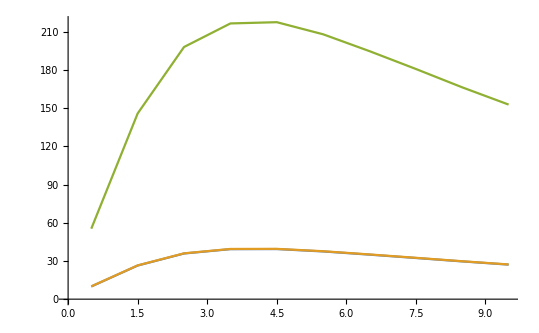

```mathematica
ListPlot[{LIST,APROX,BINLESS},Joined->True]
```

### Example of different DY - routines (Low-energy)

```mathematica
LIST={{0.12500000,0.0823915936},{0.37500000,0.2398511131},{0.62500000,0.3773572645},{0.87500000,0.4849385371},{1.12500000,0.5589483905},{1.37500000,0.5980700260},{1.62500000,0.6077850454},{1.87500000,0.5929205734},{2.12500000,0.5592551365},{2.37500000,0.5134583890}};
APROX={{0.12500000,0.0824811014},{0.37500000,0.2400937476},{0.62500000,0.3772586146},{0.87500000,0.4852373374},{1.12500000,0.5591253983},{1.37500000,0.5981712210},{1.62500000,0.6081014061},{1.87500000,0.5930123053},{2.12500000,0.5593694936},{2.37500000,0.5134761239}};
BINLESS={{0.12500000,0.0691738257},{0.37500000,0.2018225269},{0.62500000,0.3184711173},{0.87500000,0.4131644080},{1.12500000,0.4804946150},{1.37500000,0.5199804981},{1.62500000,0.5357001125},{1.87500000,0.5295290226},{2.12500000,0.5070376443},{2.37500000,0.4725925235}};
```

```mathematica
APROX⟦All,2⟧/LIST⟦All,2⟧
```

{1.00109,1.00101,0.999739,1.00062,1.00032,1.00017,1.00052,1.00015,1.0002,1.00003}

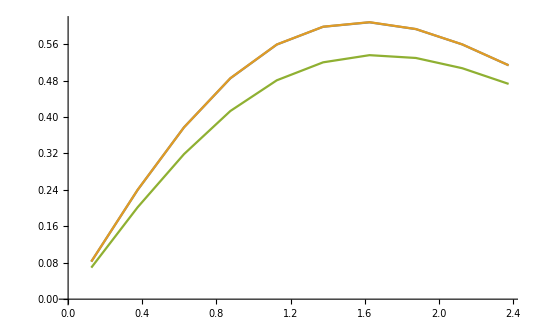

```mathematica
ListPlot[{LIST,APROX,BINLESS},Joined->True]
```

## Example.py

### Plot G0

```mathematica
G0={{1.0,0.00000000,0.00000000,0.00000000,0.00000000},{0.7943,0.00035950,0.00459224,0.00000145,0.00000098},{0.631,0.00754498,0.05569341,0.00016782,0.00013574},{0.5012,0.05331140,0.22297018,0.00092956,0.00129738},{0.3981,0.17889659,0.55096559,0.00509957,0.00740896},{0.3162,0.40603357,1.04713017,0.02432588,0.02596040},{0.2512,0.74350057,1.70042212,0.07958219,0.06695753},{0.1995,1.20123507,2.50144837,0.19743325,0.14533909},{0.1585,1.80189288,3.45622680,0.40590786,0.28581668},{0.1259,2.58140348,4.59057751,0.73576031,0.52585744},{0.1,3.58327265,5.95001543,1.22818322,0.91526866},{0.07943,4.86692800,7.60255920,1.94078683,1.51980933},{0.0631,6.51685163,9.64458023,2.96198307,2.42656627},{0.05012,8.65890486,12.21440607,4.42451250,3.75698334},{0.03981,11.46258413,15.49904946,6.50202841,5.67683606},{0.03162,15.15947480,19.75296062,9.42582313,8.41447776},{0.02512,20.06897517,25.32300042,13.50880373,12.28621966},{0.01995,26.63367481,32.68342033,19.17933711,17.73124223},{0.01585,35.46728665,42.48243944,27.02800095,25.35925903},{0.01259,47.41940412,55.60653535,37.87168714,36.01534835},{0.01,63.66276107,73.26768727,52.84076464,50.86810529},{0.007943,85.81137188,97.12292355,73.49767876,71.52977576},{0.00631,116.08128793,129.43846242,101.99832234,100.22051969},{0.005012,157.51102796,173.31576252,141.31299602,139.99363593},{0.003981,214.26472181,233.00224208,195.52931557,195.04430471},{0.003162,292.04793031,314.31524992,270.26661039,271.13050485},{0.002512,398.67084867,425.21137284,373.23652906,376.13916188},{0.001995,544.79046010,576.52942102,514.98238612,520.82851215},{0.001585,744.84057142,782.91419842,709.80912602,719.75978053},{0.001259,1018.09286481,1063.87077570,976.85232859,992.37929279},{0.001,1389.64076407,1444.76866074,1341.08621853,1364.09227245}};
```

```mathematica
pdf
```

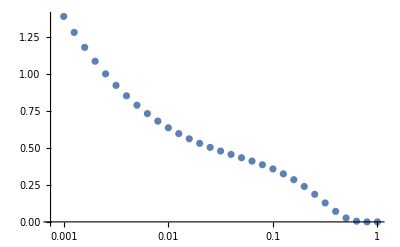

```mathematica
ListLogLinearPlot[{#⟦1⟧,#⟦1⟧#⟦2⟧}&/@G0⟦All,{1,2}⟧]
```